```mathematica
data=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/delta_phi.csv"];
```

```mathematica
histogram[{bins_,bincounts_},plotopts:OptionsPattern[]]:=Module[{width=First@Differences@bins},Graphics[{EdgeForm[Black],ColorData[97][8],Rectangle[{#1-0.5 width,0},{#1+0.5 width,#2}]&@@@Transpose[{Mean/@(Partition[bins,2,1]),bincounts}]},plotopts,Frame->True,AspectRatio->0.7]];
```

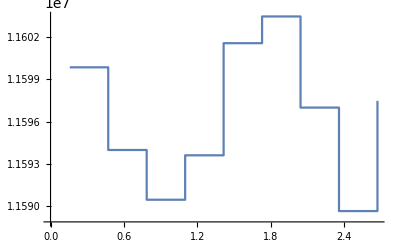

```mathematica
ListPlot[data,Joined->True,InterpolationOrder->0]
```